# Cutting a triangle by a triangle

Author : Martin Horvat, May 2016

Ref : http://mathematica.stackexchange.com/questions/528/intersecting-graphics

## Definitions

```mathematica
(* Cross product: {px,py,0} x {rx,ry,0} . k *)
Clear[Cross2D];
Cross2D[{px_,py_},{rx_,ry_}]:=px*ry -py*rx;

(* Is the point p in Triangle(r0,r1,r2)?  p,r0,r1,r2 in R^2 *)
Clear[PointInTriangle];
PointInTriangle[p_,{r0_,r1_,r2_}]:=Module[{s0,s1,s2},

(* Point is one the vertices *)
If [p==r0||p==r1||p==r2,Return[1]];

(* Point is inside the triangle *)
s0=Sign[Cross2D[p-r0,r1-r0]];
s1=Sign[Cross2D[p-r1,r2-r1]];
s2=Sign[Cross2D[p-r2,r0-r2]];

If[s0==s1==s2,Return[1]];

(* Point is on edge *)
If[(s0==0&&s1==s2)||(s1==0&&s0==s2)||s2==0&&s0==s1, Return[1]];

Return[0];
];

(* Edge intersection: Intersection between Line[p0,p1] and Line[r0,r1] *)
Clear[EdgeInter];
EdgeInter[{p0_,p1_},{r0_,r1_}]:=Module[{d,t,u},

d=Cross2D[p1-p0,r1-r0];

If[d==0,Return[None]];

u =Cross2D[p1-p0,p0-r0]/d;
t =Cross2D[r1-r0,p0-r0]/d;

If[0≤u≤1 &&0≤t≤1,Return[p0+(p1-p0)*t]];

Return[None];
];

(* Subtracting t1 from t0, Returning the set of triangles that remain. *)
Clear[SubTrig];
SubTrig[t0_,t1_]:=Module[{pit,ee,ees,n1,n2},

(* Status if the points in triangles+boundary *)
pit={
PointInTriangle[#,t0]&/@t1,
PointInTriangle[#,t1]&/@t0
};
(* Check the intersection between edges*)
ee=Outer[
EdgeInter,
Partition[Append[t0,First[t0]],2,1],
Partition[Append[t1,First[t1]],2,1],
1
];
(* ????? *)
ee
];
```

## Testing

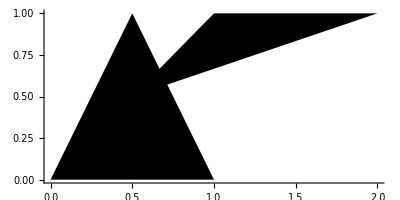

```mathematica
t1={{0,0},{1,0},{1/2,1}};
t2={{0.5,0.5},{1,1},{2,1}};

Graphics[
{
Triangle[t1],
Triangle[t2]
},
Axes->True,
BaseStyle->Directive[LightBlue,EdgeForm[Gray]]]
```